# Cardiac alternans modelled by the FitzHugh-Nagumo model

## Thu Si Nguyen Mai - s4278836 Mark Spa - s3434710

```mathematica
SetOptions[Plot,BaseStyle->{{FontFamily -> "Helvetica"}, {FontSize->13}},FrameStyle->Black, AspectRatio->Full];
SetOptions[ParametricPlot,BaseStyle->{{FontFamily -> "Helvetica"}, {FontSize->13}},FrameStyle->Black, AspectRatio->Full];
SetOptions[VectorPlot,BaseStyle->{{FontFamily -> "Helvetica"}, {FontSize->13}},FrameStyle->Black, AspectRatio->Full];
SetOptions[ListPlot,BaseStyle->{{FontFamily -> "Helvetica"}, {FontSize->13}},FrameStyle->Black, AspectRatio->Full];
SetOptions[ListLinePlot,BaseStyle->{{FontFamily -> "Helvetica"}, {FontSize->13}},FrameStyle->Black, AspectRatio->Full];
SetOptions[ContourPlot,BaseStyle->{{FontFamily -> "Helvetica"}, {FontSize->13}},FrameStyle->Black, AspectRatio->Full];
```

## Single cell receiving constant external stimulation

```mathematica
constStimulation[a_, γ_, ϵ_, Iext_, p_, tmin_, tmax_,minV_, maxV_, minw_, maxw_]:=Module[{eqV, eqw, eql, jacob, eig, sys, vars, init, solution, 
timePlot, nullClines, vectorField, phasePlot, eqlPlot, aPlot, graphs},
eqV[V_,w_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext);
eqw[V_,w_]:=V-γ*w;
eql = NSolve[{eqV[V, w] == 0.0, eqw[V, w] == 0.0}, {V, w}, Reals];
jacob = D[{eqV[V, w], eqw[V, w]}, {{V, w}}];
eig = Eigenvalues[jacob/.eql[[1]]];

sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]};
vars = {V[t], w[t]};
init = Thread[{V[tmin], w[tmin]} == p ];
solution = NDSolve[{sys, init}, vars, {t, tmin, tmax}];

timePlot = Plot[Evaluate[vars /. solution], {t, tmin, tmax}, PlotRange->{{tmin, tmax},{minV, maxV}},
			PlotStyle ->{Darker[Red],Gray},Frame -> True, FrameLabel -> {"t", "V, w"},
			PlotLabel -> Style["Time plot of constant stimulation",Black, FontSize -> 17],PlotLegends -> {"V", "w"}];

(* draw null clines *)
nullClines = ContourPlot[{eqV[V, w]== 0, eqw[V, w]== 0}, {V, minV, maxV}, {w, minw, maxw},
 ContourStyle -> {Orange, Darker[Green]},
 Frame -> True, FrameLabel -> {"V", "w"}, AspectRatio -> 1,
PlotLabel -> Style["Phase plot of constant stimulation",Black, FontSize -> 17],PlotLegends -> {"w isocline", "V isocline" } ];
 (* draw vector field *)vectorField = VectorPlot[{eqV[V, w], eqw[V, w] } , {V, minV, maxV}, {w,minw, maxw}, VectorStyle -> {Gray,"PinDart"}, VectorColorFunction->None, VectorPoints -> Fine];
phasePlot = ParametricPlot[Evaluate[vars/.solution], {t, tmin, tmax}, PlotStyle->Darker[Blue]];
(*equilibrium point*)
eqlPlot = ListPlot[{V, w} /. eql, PlotStyle -> {{Black, PointSize[0.02]}}, Frame -> True, FrameLabel -> {"V", "w"}];
(*threshold*)
(*aPlot = ListLinePlot[{{a, minw}, {a, maxw}}];*)

graphs = Row[{
Show[nullClines, vectorField, phasePlot, eqlPlot, ImageSize->Medium], 
Show[timePlot, ImageSize->{400, 300}]
}];

Column[{
Row[{"Real equilibrium at ", eql}], 
Row[{"with corresponding eigenvalues: ", eig}],
graphs}]
]

Manipulate[constStimulation[a, γ, ϵ, Iext, p,tmin, tmax, Vmin, Vmax, wmin,wmax ], 
Style["Model parameters",12],
{{a,0.2,"a"},0.0,1,.01,Appearance-> "Labeled"},
{{γ,0.4,"γ"},0.0,1,.01,Appearance-> "Labeled"},
{{ϵ,0.001,"ϵ"},0.001,1,.01, Appearance-> "Labeled"},
{{Iext,0.0,Subscript[Style["I",Italic],"stim"]},0.0,2,.01, Appearance-> "Labeled"},
Delimiter,
Style["Initial conditions",12],
{{p,{0.0,0.0},Style["p",Italic]},{-1,-1},{1,1}},
Delimiter,
Style[Row[{Style["t",Italic],", ",Style["V",Italic]," and ",Style["w",Italic]," ranges"}],12],
{{tmin,0.0,Subscript[Style["t",Italic],"min"]},0,1000,1, Appearance-> "Labeled"},
{{tmax,1.0,Subscript[Style["t",Italic],"max"]},0,1000,1, Appearance-> "Labeled"},
{{Vmin,-0.5,Subscript[Style["V",Italic],"min"]},-1,1,.01, Appearance-> "Labeled"},
{{Vmax,1.5,Subscript[Style["V",Italic],"max"]},-1,3,.01, Appearance-> "Labeled"},
{{wmin,-0.5,Subscript[Style["w",Italic],"min"]},-1,1,.01, Appearance-> "Labeled"},
{{wmax,1.5,Subscript[Style["w",Italic],"max"]},-1,3,.01, Appearance-> "Labeled"}
]
```

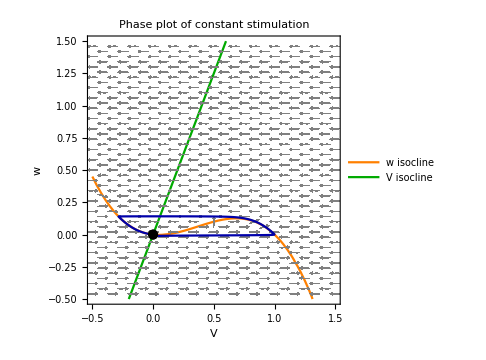
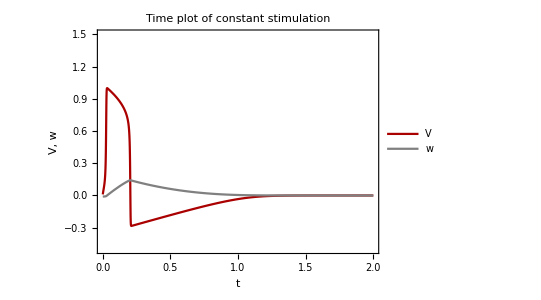
Real equilibrium at {{V→0.,w→0.}}
with corresponding eigenvalues: {-88.6713,-11.7287}
-Graphics--Graphics-

```mathematica
a=0.1; γ=0.4; ϵ=0.001; Iext=0.0; p={0.01, -0.01};tmin=0; tmax=2; Vmin=-0.5; Vmax=1.5; wmin=-0.5;wmax=1.5;
constStimulation[a, γ, ϵ, Iext, p,tmin, tmax, Vmin, Vmax, wmin,wmax]
```

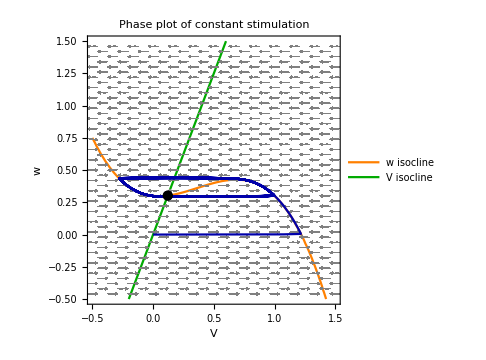
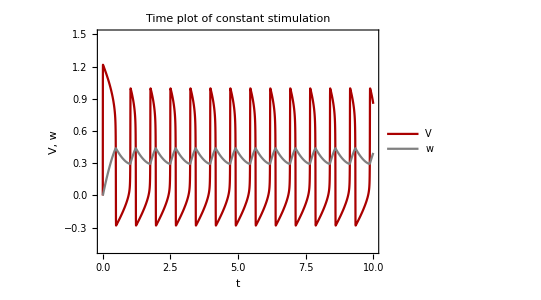
Real equilibrium at {{V→0.120888,w→0.30222}}
with corresponding eigenvalues: {113.318,8.39367}
-Graphics--Graphics-

```mathematica
a=0.1; γ=0.4; ϵ=0.001; Iext=0.3; p={0, 0};tmin=0; tmax=10; Vmin=-0.5; Vmax=1.5; wmin=-0.5;wmax=1.5;
constStimulation[a, γ, ϵ, Iext, p,tmin, tmax, Vmin, Vmax, wmin,wmax]
```

## Alternans in a single cell

## Simulation

```mathematica
periodicStimulation[a_, γ_, ϵ_, tmin_, tmax_, freq_, duration_, strength_]:=Module[{ eqV, eqw, stimuliTrain, S,
sys, vars, init, solution,
plotVw, plotPhase, plotIext,
sol, restTime, rt, drt, apds, poincare},
eqV[V_,w_,Iext_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext);
eqw[V_,w_]:=V-γ*w;

stimuliTrain[t_, A_,duty_, T_]:=A*UnitBox[Mod[t/T,1.]/(2. duty)];
S=stimuliTrain[t-(duration+1/2), strength, duration, 1/freq];

sys = {D[V[t], t] == eqV[V[t], w[t],S], D[w[t], t] == eqw[V[t], w[t]]};
vars = {V[t], w[t]};
init = Thread[{V[0], w[0]} =={0.0, 0.0}];
solution = NDSolve[{sys, init}, {V,w}, {t,tmin, tmax}];

plotVw =Plot[Evaluate[{V[t],w[t]}/.solution],{t,tmin,tmax}, PlotStyle->{Darker[Red], Gray},
Frame->True, FrameLabel -> {"t", "V, w"},PlotRange->All,
PlotLabel->Style["Time plot", Black], PlotLegends -> {"V", "w"}];
plotPhase = ParametricPlot[Evaluate[{V[t],w[t]}/.solution],{t,tmin,tmax},
Frame->True, FrameLabel -> {"V", "w"},PlotRange->All,
PlotLabel->Style["Phase plot", Black]];
plotIext = Plot[S,{t,tmin,tmax},PlotStyle->Darker[Green],ExclusionsStyle->Darker[Green],
PlotRange->{All,{0, strength+0.01}},
 Frame->True,FrameLabel -> {"t", "Stimulation"},PlotRange->All,
PlotLabel->Style["Stimulation over time", Black]];

{sol, restTime} = Reap[
NDSolve[
{sys, init, WhenEvent[V[t]==0, Sow[t]]}, 
{V,w}, {t,tmin, tmax}
]
];
rt = restTime[[1, 2;;]];
drt = Differences[rt];
apds = Pick[drt,Table[Mod[i,2],{i,1,Length@drt}],1];
poincare = ListPlot[
Table[{apds[[i]], apds[[i+1]]}, {i, 1, Length@apds-1}],
PlotStyle->{Orange, PointSize->0.02},
Frame->True, FrameLabel -> {Subscript["APD", "N"], Subscript["APD", "N+1"]},
PlotRange->{{-0.1,0.2}, {-0.1,0.2}},
PlotLabel->Style["Poincaré plot", Black]];

 Column[{
Row[{"Periodic stimulation with frequency of ", freq},BaseStyle->{{FontFamily -> "Helvetica"},{FontSize -> 17}}],
Row[{Show[plotVw, ImageSize->{500,300}], Spacer[25],Show[plotPhase, ImageSize->350, AspectRatio->1]}],
Row[{Show[ plotIext, ImageSize->{500,300}], Spacer[80], Show[poincare, ImageSize->350, AspectRatio->1]}]
}]
]
```

```mathematica
Manipulate[periodicStimulation[a, γ, ϵ, tmin, tmax,freq,duration,strength], 
Style["Model parameters",12],
{{a,0.2,"a"},0.0,1,.01,Appearance-> "Labeled"},
{{γ,0.4,"γ"},0.0,1,.01,Appearance-> "Labeled"},
{{ϵ,0.001,"ϵ"},0.001,1,.01, Appearance-> "Labeled"},
Delimiter,
{{tmin,0.0,Subscript[Style["t",Italic],"min"]},0,1000,1, Appearance-> "Labeled"},
{{tmax,5.0,Subscript[Style["t",Italic],"max"]},0,1000,1, Appearance-> "Labeled"},
Delimiter,
Style["Stimulation",12],
{{freq,1,"frequency"},0,10,0.01, Appearance-> "Labeled"},
{{duration,0.01,"duration"},0,1,0.01, Appearance-> "Labeled"},
{{strength,0.3,"strength"},0,2,0.01, Appearance-> "Labeled"}]
```

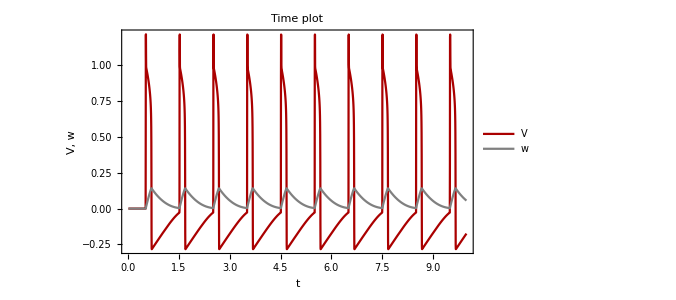
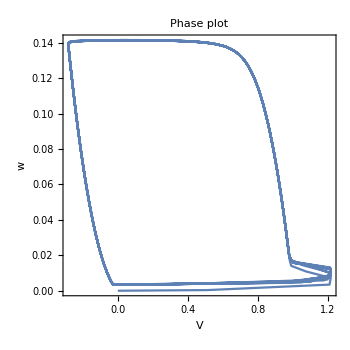
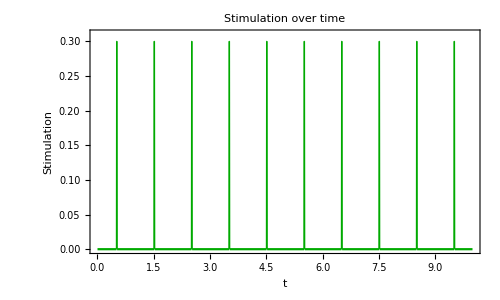
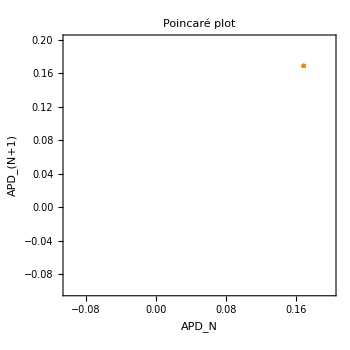
Periodic stimulation with frequency of 1.
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
a=0.1; γ=0.4; ϵ=0.001; freq=1.0; duration=0.01; strength=0.3; tmin=0; tmax=10;
periodicStimulation[a, γ, ϵ, tmin, tmax,freq,duration,strength]
```

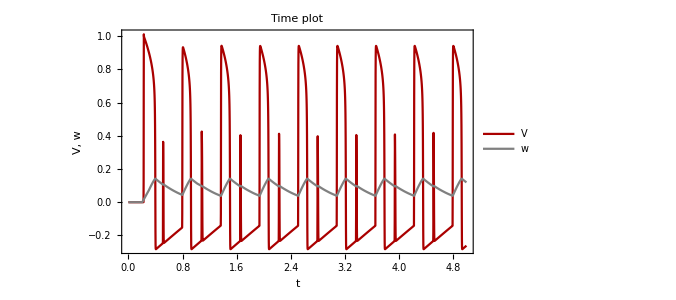
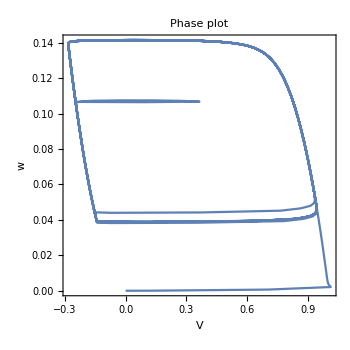
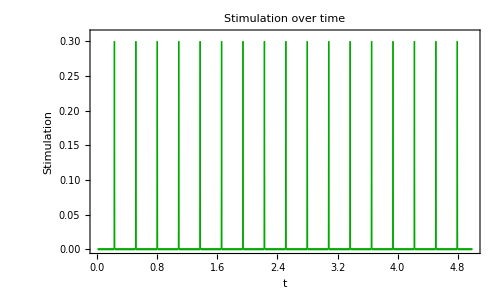
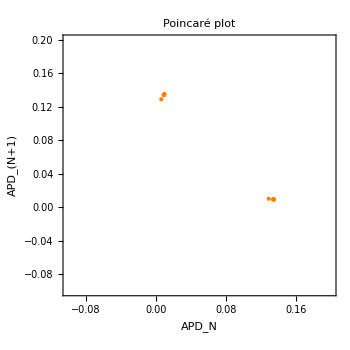
Periodic stimulation with frequency of 3.5
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
a=0.1; γ=0.4; ϵ=0.001; freq=3.5; duration=0.01; strength=0.3; tmin=0; tmax=5;
periodicStimulation[a, γ, ϵ, tmin, tmax,freq,duration,strength]
```

## System with periodic stimulation switches between sub-systems of constant stimulation

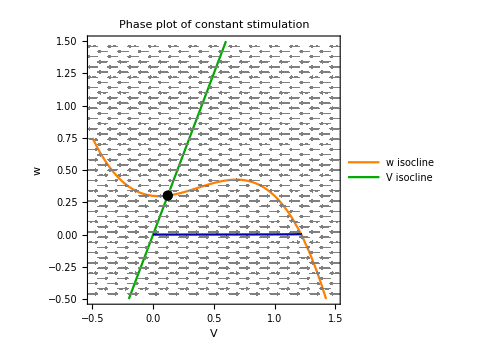
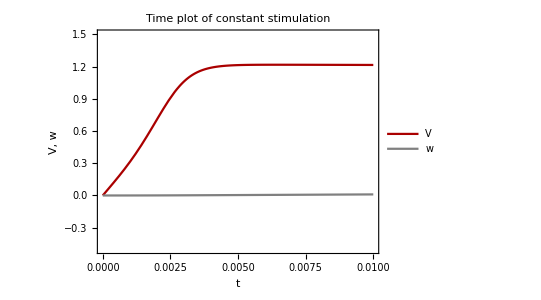
Real equilibrium at {{V→0.120888,w→0.30222}}
with corresponding eigenvalues: {113.318,8.39367}
-Graphics--Graphics-

```mathematica
a=0.1; γ=0.4; ϵ=0.001; Iext=0.3; p={0, 0};tmin=0; tmax=0.01; Vmin=-0.5; Vmax=1.5; wmin=-0.5;wmax=1.5;
constStimulation[a, γ, ϵ, Iext, p,tmin, tmax, Vmin, Vmax, wmin,wmax]
```

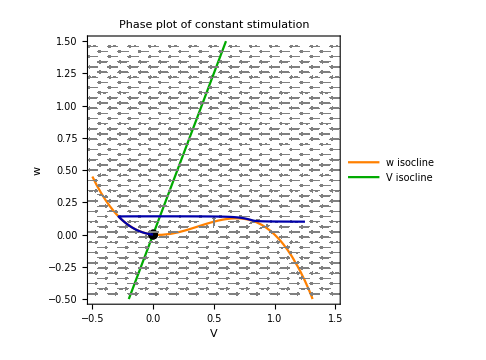
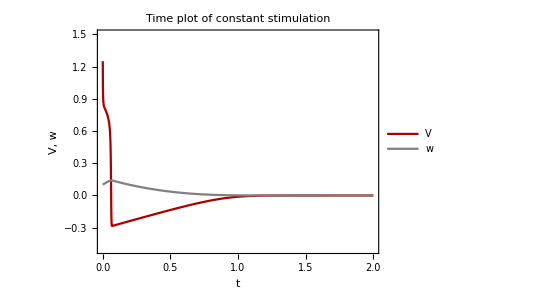
Real equilibrium at {{V→0.,w→0.}}
with corresponding eigenvalues: {-88.6713,-11.7287}
-Graphics--Graphics-

```mathematica
a=0.1; γ=0.4; ϵ=0.001; Iext=0.0; p={1.25, 0.1};tmin=0; tmax=2; Vmin=-0.5; Vmax=1.5; wmin=-0.5;wmax=1.5;
constStimulation[a, γ, ϵ, Iext, p,tmin, tmax, Vmin, Vmax, wmin,wmax]
```

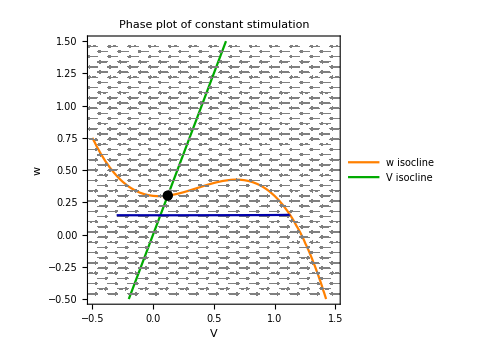
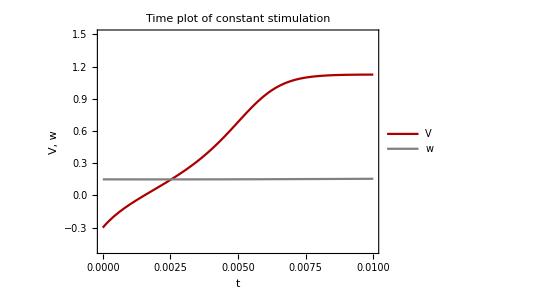
Real equilibrium at {{V→0.120888,w→0.30222}}
with corresponding eigenvalues: {113.318,8.39367}
-Graphics--Graphics-

```mathematica
a=0.1; γ=0.4; ϵ=0.001; Iext=0.3; p={-0.3, 0.15};tmin=0; tmax=0.01; Vmin=-0.5; Vmax=1.5; wmin=-0.5;wmax=1.5;
constStimulation[a, γ, ϵ, Iext, p,tmin, tmax, Vmin, Vmax, wmin,wmax]
```

## Bifurcation analysis

```mathematica
{freqs, APDs, MNs}=Reap[Do[
a=0.2; γ=0.4; ϵ=0.001; duration=0.01; strength=0.3; tmin=0; tmax=20;
restTime={};
eqV[V_,w_,Iext_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext);
eqw[V_,w_]:=V-γ*w;
stimuliTrain[t_, A_,duty_, freq_]:=A*UnitBox[Mod[t*freq,1.]/(2. duty)];

vars = {V[t], w[t]};
init = Thread[{V[0], w[0]} =={0.0, 0.0}];
S=stimuliTrain[t-(duration+1/2), strength, duration, f];
sys = {D[V[t], t] == eqV[V[t], w[t],S], D[w[t], t] == eqw[V[t], w[t]]};

NDSolve[
{sys, init, WhenEvent[V[t]==0, AppendTo[restTime,t]]}, 
{V,w}, {t,tmin, tmax}
];
rt = restTime[[2;;]];
drt = Differences[rt];
apd = Pick[drt,Table[Mod[i,2],{i,1,Length@drt}],1];
(*fapd = (Length[apd]+1)/(tmax-tmin);
mn=f/fapd ;*)
nSti=Ceiling[((tmax-tmin)-(duration+1/2))/(duration+1/f)];
mn=nSti/(Length[apd] + 1);
Sow[f, freq];
Sow[apd, apds];
Sow[mn, mns],
{f, 0.3, 15, 0.1}
]][[2]];
```

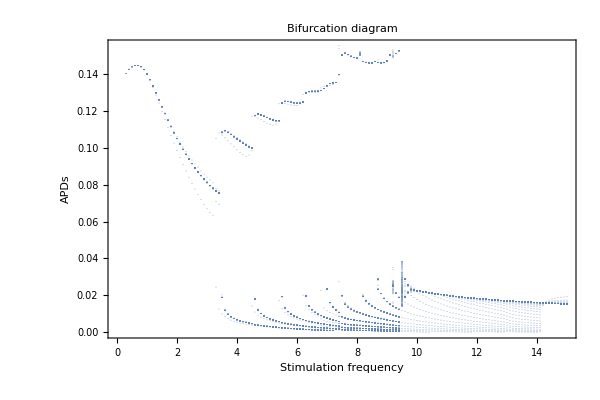

```mathematica
pts=Reap[
Do[
Sow[{freqs[[i]], APDs[[i, j]]}, p],
{i, 1, Length@freqs}, {j, 1, Length@APDs[[i]]}]
][[2,1]];
ListPlot[pts, PlotRange->All,
PlotStyle->{PointSize->0.001},
Frame->True, FrameLabel->{"Stimulation frequency", "APDs"}, 
PlotLabel->Style["Bifurcation diagram", Black, FontSize->17],
ImageSize->{600,400}]
```

```mathematica
N[MNs]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.964286,0.966667,1.,1.,1.,1.,0.975,0.97619,0.954545,0.956522,0.958333,0.96,0.961538,0.962963,0.964286,0.948276,0.95,0.951613,0.953125,0.954545,0.955882,0.942857,0.944444,0.945946,0.947368,0.961039,0.9375,0.939024,0.940476,0.94186,0.943182,0.933333,0.934783,0.93617,0.9375,0.938776,0.939394,0.931373,0.932692,0.942857,0.925926,0.927273,0.928571,0.929825,0.930435,0.923729,0.925,0.92623,0.919355,0.928,0.921875,0.915385,0.916667,0.924812,0.925926,0.919708,0.920863,0.921986,0.916084,0.917241,1.09756,1.0625,1.06154,1.0687,1.07576,1.05926,1.05839,1.06522,1.03497,1.03448,1.03401,1.03378,1.03333,1.,1.01282,1.01266,1.00625,1.01875,0.970588,0.994012,0.994083,0.904255,0.9,0.901042,0.892308,0.893401,0.894472,0.890547,0.891626,0.892683,0.888889,0.894231,0.890476,0.891509,0.88785,0.888889,0.889908,0.886364,0.887387,0.883929,0.888889,0.889868,0.886463,0.887446,0.880342,0.885106,0.881857,0.882845,0.879668,0.880658,0.881633,0.878543,0.879518,0.873016,0.87747,0.87451,0.878906,0.875969,0.876923,0.877395,0.878327,0.875472,0.876404,0.873606,0.871324,0.868613,0.869565,0.870036,0.855634,0.853147,0.854167,0.851724,0.85274,0.85034,0.851351,0.848993,0.85}

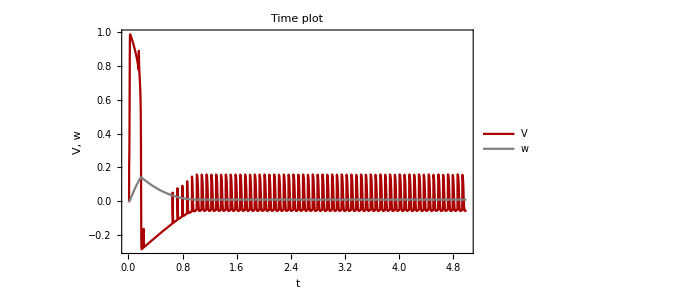
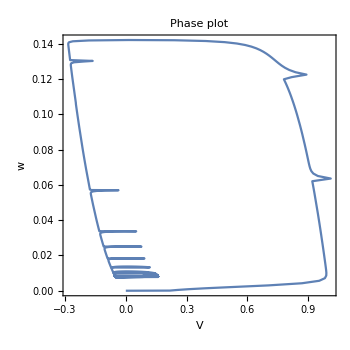
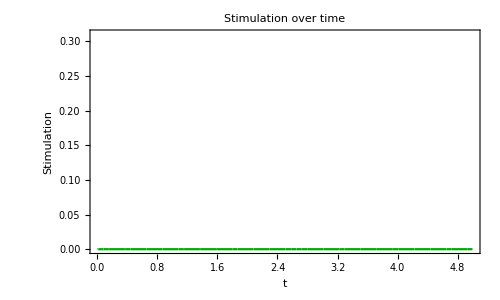
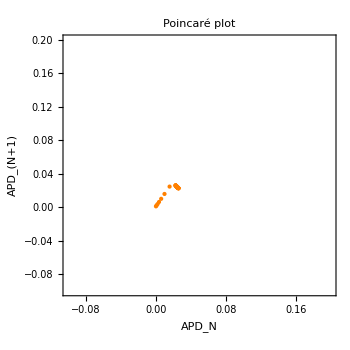
Periodic stimulation with frequency of 14
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
a=0.1; γ=0.4; ϵ=0.001; freq=14; duration=0.01; strength=0.3; tmin=0; tmax=5;
periodicStimulation[a, γ, ϵ, tmin, tmax,freq,duration,strength]
```

## Alternans in two coupled cells

```mathematica
periodicCoupledSim[a_, γ_, ϵ_, tmin_, tmax_, freq_, duration_, strength_, R_]:= Module[{ eqV1, eqw1,eqV2, eqw2,f, stimuliTrain, S,sys, vars, init, solution,plotVw, plotIext}, 
f[V_]:= V*(1-V)(V-a);
eqV1[V1_,w1_, V2_, w2_,Iext_]:=1/ϵ*(-w1+ f[V1] + (V2-V1)/R+Iext);
eqw1[V1_,w1_, V2_, w2_]:=V1-γ*w1;
eqV2[V1_,w1_, V2_, w2_]:=1/ϵ*(-w2+ f[V2] + (V1-V2)/R);
eqw2[V1_,w1_, V2_, w2_]:=V2-γ*w2;

stimuliTrain[t_, A_,duty_, f_]:=A*UnitBox[Mod[t*f,1.]/(2. duty)];
S=stimuliTrain[t-(duration+1/2), strength, duration, freq];

sys = {D[V1[t], t]==eqV1[V1[t], w1[t], V2[t], w2[t],S], 
D[w1[t], t]==eqw1[V1[t], w1[t], V2[t], w2[t]],
D[V2[t], t]==eqV2[V1[t], w1[t], V2[t], w2[t]],
D[w2[t], t]==eqw2[V1[t], w1[t], V2[t], w2[t]]};
vars = {V1[t],V2[t], w1[t],w2[t]};
init = Thread[{V1[tmin],V2[tmin],w1[tmin], w2[tmin]}=={0.0, 0.0,0.0,0.0}];

solution = NDSolve[{sys, init}, vars, {t, tmin, tmax}];

plotVw =Plot[Evaluate[{V1[t],V2[t],w1[t],w2[t]}/.solution],{t,tmin,tmax}, 
PlotStyle->{Darker[Red], Darker[Blue] , Gray, Darker[Gray]},
Frame->True, FrameLabel -> {"t", "V, w"},PlotRange->{All, {-0.5, 1}},PlotLegends -> {"V1", "V2", "w1", "w2"}];
plotIext = Plot[S,{t,tmin,tmax},
PlotStyle->Darker[Green],ExclusionsStyle->Darker[Green],
PlotRange->{All,{0, strength+0.01}}, Frame->True,FrameLabel -> {"t", "Stimulation"},PlotRange->All];

 Column[{
Row[{
Spacer[51],"Periodic stimulation with frequency of " ,Style[freq,Bold],  
"\n           and coupling strength ", Style[1/R, Bold]},
BaseStyle->{{FontFamily->"Helvetica"},{FontSize->17}}],
Column[{Show[plotVw,ImageSize->{362,200}], 
Show[ plotIext, ImageSize->{362,200}]}]
}]
]
```

```mathematica
Manipulate[periodicCoupledSim[a, γ, ϵ, tmin, tmax,freq,duration,strength, resistance], 
Style["Model parameters",12],
{{a,0.1,"a"},0.0,1,.01,Appearance-> "Labeled"},
{{γ,0.5,"γ"},0.0,1,.01,Appearance-> "Labeled"},
{{ϵ,0.008,"ϵ"},0.001,1,.01, Appearance-> "Labeled"},
Delimiter,
{{tmin,0.0,Subscript[Style["t",Italic],"min"]},0,1000,1, Appearance-> "Labeled"},
{{tmax,5.0,Subscript[Style["t",Italic],"max"]},0,1000,1, Appearance-> "Labeled"},
Delimiter,
Style["Stimulation",12],
{{freq,1,"frequency"},0,10,0.01, Appearance-> "Labeled"},
{{duration,0.1,"duration"},0,1,0.01, Appearance-> "Labeled"},
{{strength,0.025,"strength"},0,2,0.01, Appearance-> "Labeled"},
{{resistance,45,"resistance"},0.1,100,1, Appearance-> "Labeled"}]
```

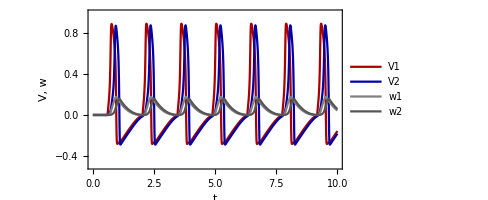
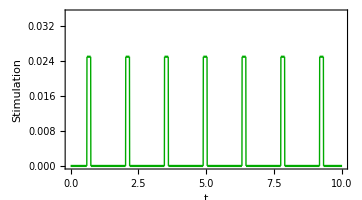
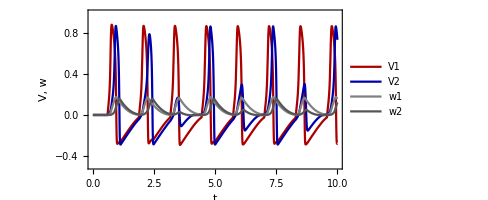
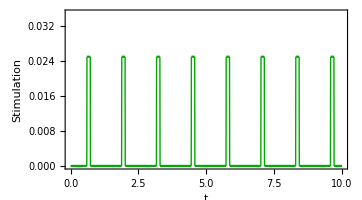
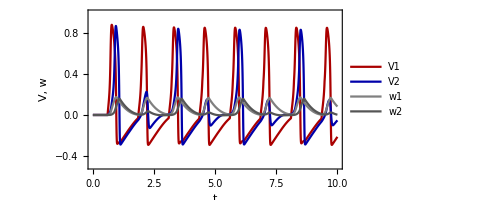
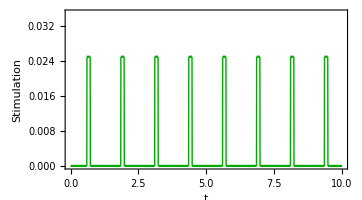
Periodic stimulation with frequency of 0.7
           and coupling strength 1/45
-Graphics-
-Graphics-Periodic stimulation with frequency of 0.78
           and coupling strength 1/45
-Graphics-
-Graphics-Periodic stimulation with frequency of 0.8
           and coupling strength 1/45
-Graphics-
-Graphics-

```mathematica
a=0.1; γ=0.5; ϵ=0.008; duration=0.1; strength=0.025; resistance=45; 
tmin=0; tmax=10;
pA=periodicCoupledSim[a, γ, ϵ, tmin, tmax,0.7,duration,strength, resistance];
pB=periodicCoupledSim[a, γ, ϵ, tmin, tmax,0.78,duration,strength, resistance];
pC=periodicCoupledSim[a, γ, ϵ, tmin, tmax,0.8,duration,strength, resistance];
Row[{pA, pB, pC}]
```

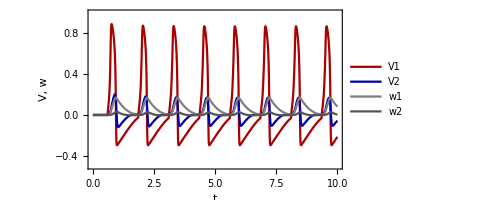
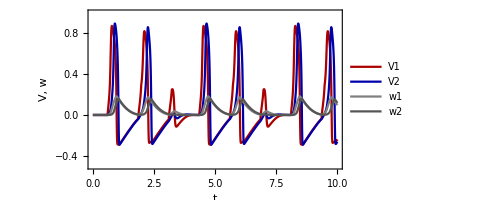
Periodic stimulation with frequency of 0.8
           and coupling strength 1/55
-Graphics-
-Graphics-Periodic stimulation with frequency of 0.8
           and coupling strength 1/45
-Graphics-
-Graphics-Periodic stimulation with frequency of 0.8
           and coupling strength 1/35
-Graphics-
-Graphics-

```mathematica
a=0.1; γ=0.5; ϵ=0.008; duration=0.1; strength=0.025; freq=0.8; 
tmin=0; tmax=10;
pA=periodicCoupledSim[a, γ, ϵ, tmin, tmax,freq,duration,strength, 55];
pB=periodicCoupledSim[a, γ, ϵ, tmin, tmax,freq,duration,strength, 45];
pC=periodicCoupledSim[a, γ, ϵ, tmin, tmax,freq,duration,strength, 35];
Row[{pA, pB, pC}]
```

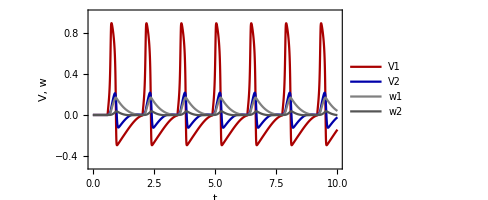
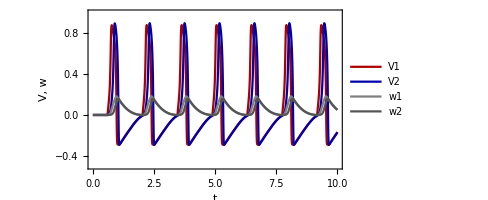
Periodic stimulation with frequency of 0.7
           and coupling strength 1/55
-Graphics-
-Graphics-Periodic stimulation with frequency of 0.7
           and coupling strength 1/45
-Graphics-
-Graphics-Periodic stimulation with frequency of 0.7
           and coupling strength 1/35
-Graphics-
-Graphics-

```mathematica
a=0.1; γ=0.5; ϵ=0.008; duration=0.1; strength=0.025; freq=0.7; 
tmin=0; tmax=10;
pA=periodicCoupledSim[a, γ, ϵ, tmin, tmax,freq,duration,strength, 55];
pB=periodicCoupledSim[a, γ, ϵ, tmin, tmax,freq,duration,strength, 45];
pC=periodicCoupledSim[a, γ, ϵ, tmin, tmax,freq,duration,strength, 35];
Row[{pA, pB, pC}]
```

## Alternans in the spatial FHN model of a cardiac tissue

## Base codes for both sections below

```mathematica
makeSystem[A_, a_List,γ_List, ϵ_List]:=Module[{n=Length[A], varsV,varsw, lhsV, rhsV, lhsw, rhsw}, (*n here is the total number of heart cells*)
varsV=Table[Subscript[V, i][t],{i,1,n}];
varsw=Table[Subscript[w, i][t],{i,1,n}];
lhsV=D[varsV,t];
rhsV=Table[varsV[[i]](varsV[[i]]-a[[i]])(1-varsV[[i]])-varsw[[i]],{i,1,n}];
rhsV+=(A-DiagonalMatrix[Total/@A]).varsV;
lhsw=D[varsw,t];
rhsw=Table[varsV[[i]]-γ[[i]]varsw[[i]],{i,1,n}];

Join[Thread[lhsV==ϵ^-1 rhsV],Thread[lhsw==rhsw]]
]
makeSphereConnectionMatrix[n_,α_]:=Module[{i,j,k0, kEast, kWest, kNorth, kSouth}, (*n = size of the spatial grid => the total number of heart cells = n^2*)
getIndex[i_,j_]:=i n+j; (*get index of a heart cell given its position (row i, column j) in the spatial grid*)
A=Table[0,n^2,n^2];
Do[Do[
k =getIndex[i ,j]; (*index of the focal cell*)
kSouth=getIndex[Mod[i+1,n], j]; (*index of southern adjacent cell*)
kNorth=getIndex[Mod[i+n-1,n], j]; (*index of northern adjacent cell*)
kEast=getIndex[i, Mod[j+1,n]]; (*index of eastern adjacent cell*)
kWest=getIndex[i, Mod[j+n-1,n]]; (*index of western adjacent cell*)
A[[k+1,kSouth+1]]=α;
A[[k+1,kNorth+1]]=α;
A[[k+1,kEast+1]]=α;
A[[k+1,kWest+1]]=α
,{j, 0, n-1}],{i,0,n-1}];
SparseArray[A]
]

stimuliTrain[t_, A_,duty_, freq_]:=A*UnitBox[Mod[t*freq,1.]/(2. duty)]
stiGrid[τ_, s_List, S_List, n_]:= Module[{sm, i, j},
sm=Table[0,n,n];
Do[
i= Ceiling[s[[k]]/n];
j=Mod[s[[k]]-1, n]+1;
sm[[i, j]]=S[[k]]
,{k, 1, Length[s]}];
sm
]

colorA = ColorData[97,"ColorList"][[{1, 10, 9, 15}]];
colorB = Join[ColorData[97,"ColorList"][[{8, 4}]], {Brown}];
colorC = {Pink, Gray};

n=7; (*size of the spatial grid*)
aList = Table[0.01, Length@cMatrix];
γList = Table[0.5, Length@cMatrix];
ϵList = Table[0.008, Length@cMatrix];
duration=0.1;  strength=0.05 ;
```

## Scenario (1): 1 single cells receiving external stimulation (cell number 1 in the upper-left corner)

```mathematica
spatialSim[A_, a_List,γ_List, ϵ_List, duration_, strength_, frequency_, sDelay_List, tmin_, tmax_, tStep_]:= Module[
{n=Sqrt[Length[A]],ODEsys, s, delay, S, vars,initLHS, init, solution, m, cellsPlots, stiPlots, dynamicPlots, staticPlots},
ODEsys = makeSystem[A, a, γ, ϵ];

s=sDelay[[1]]; delay=sDelay[[2]];
S=stimuliTrain[t+delay, strength, duration, frequency];
ODEsys[[s, 2]]+= S*ϵ[[1]]^-1;

(*Solve system*)
vars = Integrate[ODEsys[[All, 1]], t];
initLHS =  vars/.t->tmin ;
init = Thread[initLHS== Table[0, Length@ODEsys]];
solution = NDSolve[{ODEsys, init}, vars, {t, tmin, tmax}][[1]];

staticPlots=Plot[Evaluate[{Subscript[V, 1][t],Subscript[V, n^2][t],Subscript[V, Ceiling[n^2/2]][t]}/.solution],{t,tmin,tmax},PlotRange->All,
			Frame->True, FrameLabel->{"t", "V"}, PlotLegends->{"V_1", Subscript["V", n^2], Subscript["V", Ceiling[n^2/2]]}];

m = Table[Subscript[V, (i-1) n+j][t]/.solution,{i,1,n},{j,1,n}];
cellsPlots= Table[MatrixPlot[m,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1}]]&),ColorFunctionScaling->False,
						ImageSize->400],{t,tmin,tmax,tStep}];
stiPlots = Table[MatrixPlot[stiGrid[t, {s}, {S}, n], ColorFunction->(ColorData[{"PigeonTones", "Reverse"}][Rescale[#,{0,0.2}]]&),ColorFunctionScaling->False,
								ImageSize->400], 
					{t, tmin, tmax, tStep}];
dynamicPlots = Table[
Row[{
Column[{Style["Voltages of cells", FontSize->15], cellsPlots[[i]]}],
"    ", 
 Column[{Style["Stimulation", FontSize->15], stiPlots[[i]]}]
}], 
{i, 1, Length@cellsPlots}];

{staticPlots, dynamicPlots}
]
```

```mathematica
cMatrix = makeSphereConnectionMatrix[n, 1/30];
MatrixForm[cMatrix];
frequency=0.88;
tmin=0; tmax=20; tStep=0.05;
sDelay={1, 0.2};
sim1 = spatialSim[cMatrix, aList, γList, ϵList, duration, strength, frequency, sDelay, tmin, tmax, tStep];
```

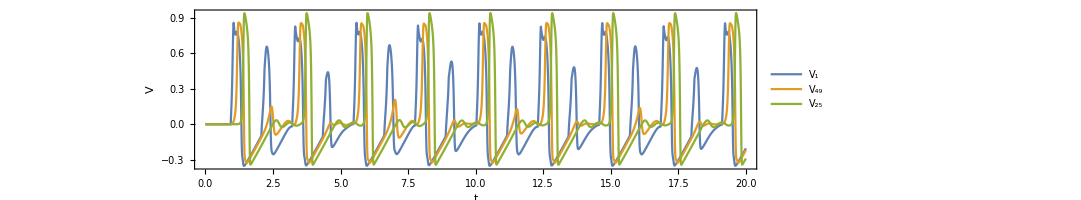
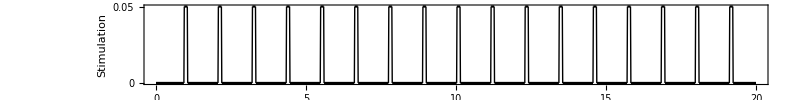
Simulation frequency = 0.88
-Graphics-
-Graphics-

```mathematica
ps = Plot[stimuliTrain[t+sDelay[[2]], strength, duration, frequency], {t, tmin, tmax},
PlotStyle->Black, ExclusionsStyle->True,
Frame->True, FrameLabel->{"t", "Stimulation"}];
Column[{
Row[{"Simulation frequency = ", Style[frequency, Bold]}, BaseStyle->{{FontFamily->"Helvetica"}, {FontSize->15}}],
Show[sim1[[1]], ImageSize->{800,200}],
 Show[ps, ImageSize->{800,100}, FrameTicks->{{{0, 0.025, 0.05},None},{{0, 5, 10, 15, 20}, None}}]
}]
```

```mathematica
ListAnimate[sim1[[2]]]
```

## Scenario (2): 2 cells receiving external stimulation

```mathematica
spatialSim2Sources[A_, a_List,γ_List, ϵ_List, duration_, strength_, frequency_, sDelay_List, tmin_, tmax_, tStep_]:= Module[
{n=Sqrt[Length[A]],ODEsys, s, delay, S, SS,vars,initLHS, init, solution, m, cellsPlots, stiPlots, dynamicPlots},
ODEsys = makeSystem[A, a, γ, ϵ];

S={};
Do[
s=sDelay[[k,1]]; delay=sDelay[[k,2]];
SS=stimuliTrain[t+delay, strength, duration, frequency];
S=AppendTo[S, SS];
ODEsys[[s, 2]]+= SS*ϵ[[1]]^-1
,{k, 1, Length[sDelay]}];

(*Solve system*)
vars = Integrate[ODEsys[[All, 1]], t];
initLHS =  vars/.t->tmin ;
init = Thread[initLHS== Table[0, Length@ODEsys]];
solution = NDSolve[{ODEsys, init}, vars, {t, tmin, tmax}][[1]];

m = Table[Subscript[V, (i-1) n+j][t]/.solution,{i,1,n},{j,1,n}];
cellsPlots= Table[MatrixPlot[m,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1}]]&),ColorFunctionScaling->False,
						ImageSize->400],{t,tmin,tmax,tStep}];
stiPlots = Table[MatrixPlot[stiGrid[t, sDelay[[All, 1]], S, n], ColorFunction->(ColorData[{"PigeonTones", "Reverse"}][Rescale[#,{0,0.2}]]&),ColorFunctionScaling->False,
								ImageSize->400], 
					{t, tmin, tmax, tStep}];
dynamicPlots = Table[
Row[{
Column[{Style["Voltages of cells", FontSize->15], cellsPlots[[i]]}],
"    ", 
 Column[{Style["Stimulation", FontSize->15], stiPlots[[i]]}]
}], 
{i, 1, Length@cellsPlots}];

{solution, dynamicPlots}
]
```

```mathematica
cMatrix = makeSphereConnectionMatrix[n, 1/100];
MatrixForm[cMatrix];
frequency=88/100;
tmin=0;tmax=30;tStep=0.05;
sDelay={{(2-1)n+2,1/frequency/20}, {(5-1)n+5, 1/frequency/7}};
sim2 = spatialSim2Sources[cMatrix, aList, γList, ϵList, duration, strength, frequency, sDelay, tmin, tmax, tStep];
```

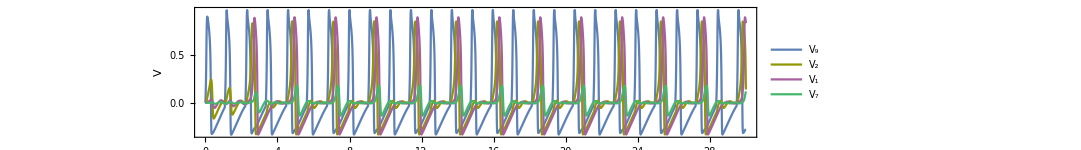
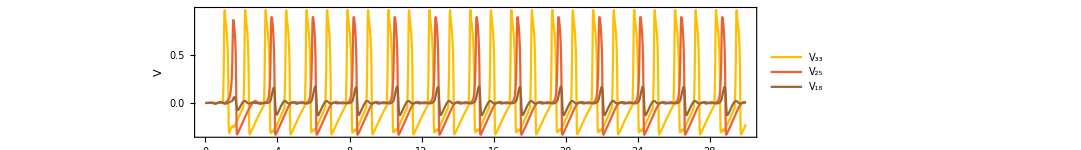
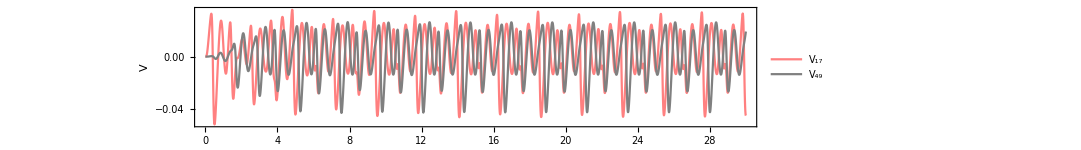
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
statPlotsA=Plot[Evaluate[{Subscript[V, 9][t],Subscript[V, 2][t],Subscript[V, 1][t], Subscript[V, 7][t]}/.sim2[[1]]],{t,tmin,tmax},PlotRange->All,
			PlotStyle->colorA,
			Frame->True, FrameLabel->{None, "V"}, PlotLegends->{"V_9", "V_2", "V_1", "V_7"}];
statPlotsB=Plot[Evaluate[{Subscript[V, 33][t],Subscript[V, 25][t],Subscript[V, 18][t]}/.sim2[[1]]],{t,tmin,tmax},PlotRange->All,
			PlotStyle->colorB,
			Frame->True, FrameLabel->{None, "V"}, PlotLegends->{"V_33", "V_25", "V_18"}];
statPlotsC=Plot[Evaluate[{Subscript[V, 17][t],Subscript[V, 49][t]}/.sim2[[1]]],{t,tmin,tmax},PlotRange->All,
			PlotStyle->colorC,
			Frame->True, FrameLabel->{"t", "V"}, PlotLegends->{"V_17", "V_49"}];

ps1 = Plot[stimuliTrain[t+sDelay[[1,2]], strength, duration, frequency], {t, tmin, tmax}, 
PlotStyle->colorA[[1]],ExclusionsStyle->colorA[[1]],
Frame->True, FrameLabel->{None, "Stimulation"}];
ps2 = Plot[stimuliTrain[t+sDelay[[2,2]], strength, duration, frequency], {t, tmin, tmax}, 
PlotStyle->colorB[[1]],ExclusionsStyle->colorB[[1]],
Frame->True, FrameLabel->{None, "Stimulation"}];

Column[{
Show[statPlotsA, ImageSize->{800,150}],
Show[ps1, ImageSize->{800,90}], 
Show[statPlotsB, ImageSize->{800,150}],
Show[ps2, ImageSize->{800,90}],
Show[statPlotsC, ImageSize->{800,150}]
}]
```

```mathematica
ListAnimate[sim2[[2]]]
```